```mathematica
DiMauro={{0.11592770333719869 ,1.430902724036737*10^-7 },{0.1552419727919801,1.3179420496721543*10^-7},{0.20454943547538015,8.583697005721025*10^-8},{0.2761483125230999,9.429532155412788*10^-8},{0.36803607894880785,1.5174694782872762*10^-7},{0.48679704343252744,2.3027136175334634*10^-7},{0.6526663609063482,2.762615710198307*10^-7},{0.868657027321059,3.2949591880051146*10^-7},{1.164235975134054,3.6624168819479853*10^-7},{1.5487794318504893,3.9298828318905065*10^-7},{2.073515175360936,3.4332619284070296*10^-7},{2.756110370684767,3.0707058382385326*10^-7},{3.6645869109432856,2.9470080134723354*10^-7},{4.938211547069397,2.15863437995542*10^-7},{6.609896317259527,1.7992791265356413*10^-7},{8.653956168958699,1.4393323808133127*10^-7},{11.585659239935609,1.250078960579582*10^-7},{15.282166070975402,1.0358715668866392*10^-7},{20.457126458496873,8.787762697302056*10^-8},{27.388854044575474,7.722477322409351*10^-8},{36.36344700262212,5.3653189668710636*10^-8},{48.734279516882474,5.8940160269446834*10^-8},{65.21964092744737,4.714914987619674*10^-8},{86.75685271001828,5.000157918665334*10^-8}};
Zhong12={{0.2698936461850911,2.0235896477251556*10^-8},{0.4031852049908963,5.55773658648687*10^-8},{0.5306041497635453,8.286427728546843*10^-8},{0.6836949708649847,9.319395762340776*10^-8},{0.8809558187480787,7.722449945836255*10^-8},{1.1593649950439693,1.2067926406393264*10^-7},{1.493866975713819,1.2949258422052604*10^-7},{1.965974958149487,1.52641796717523*10^-7},{2.5332014314857654,1.4563484775012414*10^-7},{3.3337711183217964,1.5627069765469932*10^-7},{4.205844492778353,1.4563484775012414*10^-7},{7.284258025108297,8.68511373751352*10^-8},{51.951289318465555;3.23745754281764*10^-8}};
Zhong1={{0.2756556969794437;2.5595479226995333*10^-8},{0.41179294238496555;7.906043210907701*10^-8},{0.5306041497635453;1.2648552168552957*10^-7},{0.6836949708649847;1.5998587196060571*10^-7},{0.8809558187480787;1.389495494373136*10^-7},{1.1593649950439693;1.8420699693267125*10^-7},{1.525760047357919;1.8858632787726476*10^-7},{1.965974958149487;1.9765980717016307*10^-7},{2.5332014314857654;1.7575106248547896*10^-7},{3.3337711183217964;1.8858632787726476*10^-7},{4.295636490267305;1.7992936232915516*10^-7},{7.439772114947442;1.0730309405261565*10^-7},{51.951289318465555;3.906939937054621*10^-8}};
```

```mathematica
(*Let's create a matrix with error bars!*)
Clear[Calore];
Calore={{0.3204486923217852,6.9564960995706185*10^-9},{0.3759635927148633,5.6521774773949544*10^-8},{0.41753189365604004,5.870937850692427*10^-8},{0.4605597747647078,7.425886368281534*10^-8},{0.5224596297751556,8.28642772854686*10^-8},{0.5844323938042159,2.0879874845047515*10^-7},{0.6556985133819497,2.5967438685878555*10^-7},{0.7475885795969246,2.0574088705192087*10^-7},{0.8531678524172814,2.9935772947204905*10^-7},{0.9855215688383892,2.9648599685278553*10^-7},{1.1387901130668405,3.4600097472326136*10^-7},{1.3317708758407547,3.6002561319062116*10^-7},{1.6149512770943755,3.2538091209159305*10^-7},{1.9291989145345407,3.9859764927376447*10^-7},{2.2947423401149027,3.541113510035906*10^-7},{2.926352575600284,3.3897972273636966*10^-7},{3.737141937450008,3.316333172539281*10^-7},{5.094806239666136,2.909218779465988*10^-7},{7.157154694129966,1.7752688336350715*10^-7},{10.018497226843353,2.1426863106901705*10^-7},{15.794220821098424,1.0308061514091419*10^-7},{28.193766915612823,9.411434162314103*10^-8},{62.79922353366887,5.360538616292313*10^-8}};
CaloreYBars={{5.261243901795341*10^-9,1.2451970847350344*10^-7},{4.3596917354484804*10^-8,1.7033053754470635*10^-7},{4.641588833612782*10^-8,1.757510624854793*10^-7},{5.779692884153325*10^-8,1.9006912028137782*10^-7},{6.449466771037634*10^-8,1.871151032297162*10^-7},{8.96150501946605*10^-8,3.212201060091675*10^-7},{1.3051074191219142*10^-7,3.786441858286776*10^-7},{9.691579392800497*10^-8,3.137607680703797*10^-7},{1.8134408785428515*10^-7,4.0312726942699733*10^-7},{1.9611779729377534*10^-7,3.906939937054621*10^-7},{2.1884471064600324*10^-7,4.4285189092265933*10^-7},{2.641001862504401*10^-7,4.498432668969444*10^-7},{2.3667351447252376*10^-7,4.159562163071843*10^-7},{3.0888435964774847*10^-7,4.789300737773289*10^-7},{2.811768697974231*10^-7,4.3596917354484804*10^-7},{2.5999559286685494*10^-7,4.159562163071843*10^-7},{2.641001862504401*10^-7,3.968619443383443*10^-7},{2.329951810515372*10^-7,3.584443743672719*10^-7},{1.2648552168552957*10^-7,2.258091295300894*10^-7},{1.5505157798326253*10^-7,2.5999559286685494*10^-7},{5.689866029018305*10^-8,1.5026946780037864*10^-7},{6.153407071116611*10^-8,1.2451970847350344*10^-7},{2.1544346900318866*10^-8,8.28642772854686*10^-8}};

(*ErrorCalore=Total[{Calore,CaloreERR.DiagonalMatrix[{0,-1}]}]*)


(*We want to interpolate using the following function*)
```

{{-1.69525×10^-9,1.17563×10^-7},{-1.29249×10^-8,1.13809×10^-7},{-1.22935×10^-8,1.17042×10^-7},{-1.64619×10^-8,1.1581×10^-7},{-1.83696×10^-8,1.04251×10^-7},{-1.19184×10^-7,1.12421×10^-7},{-1.29164×10^-7,1.1897×10^-7},{-1.08825×10^-7,1.0802×10^-7},{-1.18014×10^-7,1.0377×10^-7},{-1.00368×10^-7,9.4208×10^-8},{-1.27156×10^-7,9.68509×10^-8},{-9.59254×10^-8,8.98177×10^-8},{-8.87074×10^-8,9.05753×10^-8},{-8.97133×10^-8,8.03324×10^-8},{-7.29345×10^-8,8.18578×10^-8},{-7.89841×10^-8,7.69765×10^-8},{-6.75331×10^-8,6.52286×10^-8},{-5.79267×10^-8,6.75225×10^-8},{-5.10414×10^-8,4.82822×10^-8},{-5.92171×10^-8,4.5727×10^-8},{-4.6182×10^-8,4.71889×10^-8},{-3.25803×10^-8,3.04054×10^-8},{-3.2061×10^-8,2.92589×10^-8}}

FittedModel[9.26854×10^-8 (Piecewise[{{2.79056 x^0.58, x<2.06}, {6.69069/x^0.63, x>2.06}, {0, True}}])]

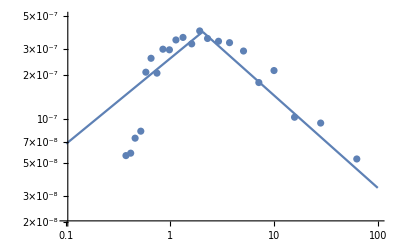

1.81217×10^-9

1.52914×10^-9

1.81217×10^-9

```mathematica
(*Simple FIT to get some initial values for ROOT; USING CALORE ET AL TECHNIQUE*)
POINTS=Calore;
(*PointsErrors=ErrorCalore . {0,1};*)
PointsErrors=(CaloreYBars+Calore.{0,-1})

Eb=2.06 GeV;
n1=1.42;
n2=2.63;
GeV=1; (*GeV=0.00160218 erg*)

Clear[F1,F];
F[x_]=Piecewise[{{x^2 (x/Eb)^-n1,x<Eb},{x^2 (x/Eb)^-n2,x>Eb}}];
F1=NonlinearModelFit[POINTS,F0  F[x],F0,x,Weights->1/(PointsErrors.{1,1})^2,VarianceEstimatorFunction->(1&)]
(*F1[x_]=Fit[DiMauro,F[x],x]*)

Show[ListLogLogPlot[POINTS,PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}],
LogLogPlot[F1[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}]]

NIntegrate[F1[x]/x,{x,0.1,100}] 0.00160218
NIntegrate[F1[x]/x,{x,0.1,10}] 0.00160218
```

FittedModel[Piecewise[{{2.38935×10^-7 x^0.394702, x<3.11054}, {(8.92166×10^-7)/x^0.766264, x>3.11054}, {0, True}}]]

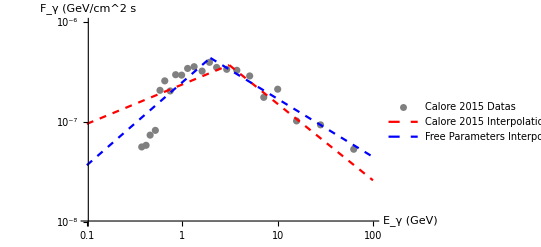

1.85419×10^-9

1.58939×10^-9

```mathematica
(*Simple FIT to get some initial values for ROOT; USING FREE PARAMETERS*)
Clear[F0,n1,n2,Eb,POINTS];
POINTS=Calore;
PointsErrors=(CaloreYBars+Calore.{0,-1}).{1,1};

F[x_]=  Piecewise[{{F0 (x/Eb)^-n1,x<Eb},{F0 (x/Eb)^-n2,x>Eb}}];
F1=NonlinearModelFit[POINTS,{F[x],Eb>0},{F0,{n1,1.41},{n2,2.63},{Eb,2.06}},x,Weights->1/PointsErrors^2,VarianceEstimatorFunction->(1&)]
Show[ListLogLogPlot[POINTS,PlotRange->{{10^-1,10^2},{10^-8,10^-6}},PlotStyle->Gray,PlotLegends->{"Calore 2015 Datas"},AxesLabel->{"E_γ (GeV)","F_γ (GeV/cm^2 s"}],
LogLogPlot[F1[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{10^-8,10^-6}},PlotStyle->{Red,Dashed},PlotLegends->{"Calore 2015 Interpolation"}],LogLogPlot[F2[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{10^-8,10^-6}},PlotStyle->{Blue,Dashed},PlotLegends->{"Free Parameters Interpolation"}]]
NIntegrate[F1[x]/x,{x,0.1,100}] 0.00160218
NIntegrate[F1[x]/x,{x,0.1,10}] 0.00160218
```

FittedModel[Piecewise[{{2.94163×10^-7 x^0.455388, x<2.06}, {(6.68131×10^-7)/x^0.679722, x>2.06}, {0, True}}]]

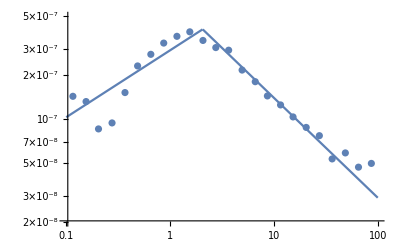

3.92597×10^-7 (Piecewise[{{0.743557 x^0.41, x<2.06}, {1.57665/x^0.63, x>2.06}, {0, True}}])

```mathematica
(*By keeping Eb constant at 2.06 we can make a new fit*)
Clear[F0,n1,n2];
Eb=2.06;
F[x_]=Piecewise[{{x^2  F0 (x/Eb)^-n1,x<Eb},{x^2  F0 (x/Eb)^-n2,x>Eb}}];
F1=NonlinearModelFit[DiMauro,F[x],{F0,n1,n2},x]
Show[ListLogLogPlot[DiMauro,PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}],
LogLogPlot[F1[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}]]
```

```mathematica
PointsErrors// MatrixForm
```

1.94301×10^-9

1.63954×10^-9

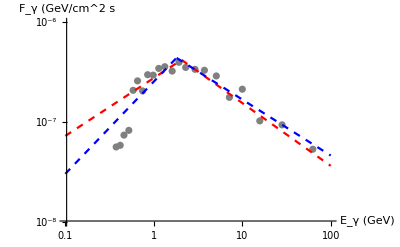

```mathematica
(*See the ROOT Results [Calore Method]*)
Clear[F0,n1,n2,Eb,POINTS,F1];
POINTS=Calore;
Eb=2.06 GeV;
n1=1.42;
n2=2.63;
GeV=1; (*GeV=0.00160218 erg*)
F0=9.9377 10^-8;
F1[x_]=F0 Piecewise[{{x^2 (x/Eb)^-n1,x<Eb},{x^2 (x/Eb)^-n2,x>Eb}}];
CaloreB=NIntegrate[F1[x]/x,{x,0.1,100}] 0.00160218
CaloreS=NIntegrate[F1[x]/x,{x,0.1,10}] 0.00160218

Show[ListLogLogPlot[POINTS,PlotRange->{{10^-1,10^2},{10^-8,10^-6}},PlotStyle->Gray,PlotLegends->Placed[{"Calore 2015 Datas"},{Right,Top}],AxesLabel->{"E_γ (GeV)","F_γ (GeV/cm^2 s"}],
LogLogPlot[F1[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{10^-8,10^-6}},PlotStyle->{Red,Dashed},PlotLegends->Placed[{"Calore 2015 Interpolation"},{Right,Top}]],LogLogPlot[F2[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{10^-8,10^-6}},PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"Free Parameters Interpolation"},{Right,Top}]]]
```

```mathematica
(*See the ROOT Results [FreeFit Method]*)
Clear[F0,n1,n2,Eb,POINTS,F0,F1];
Eb=1.80840GeV;
n1=-9.23923 10^-1;
n2=5.61343 10^-1;
GeV=1; (*GeV=0.00160218 erg*)
F0=4.41171 10^-7;
F2[x_]=F0 Piecewise[{{(x/Eb)^-n1,x<Eb},{ (x/Eb)^-n2,x>Eb}}];
FreeB=NIntegrate[F2[x]/x,{x,0.1,100}] 0.00160218
FreeS=NIntegrate[F2[x]/x,{x,0.1,10}] 0.00160218
```

1.83911×10^-9

1.48935×10^-9

```mathematica
(*Direct Numerical Integration*)
Clear[POINTS,F1];
POINTS=Calore;
F1=Interpolation[POINTS,InterpolationOrder->2];
DirectB=NIntegrate[F1[x]/x,{x,0.35,62}] 0.00160218
DirectS=NIntegrate[F1[x]/x,{x,0.35,10}] 0.00160218
```

1.71036×10^-9

1.40855×10^-9

```mathematica
Show[DataB=BarChart[{{DirectB,CaloreB,FreeB}},ChartLegends->Placed[{"Direct Numerical Integration","Calore Fit","Power Law Fit"},{Right,Top}],ChartStyle->"DarkRainbow",AxesLabel->{"","F_γ"},BarSpacing->None],
DataS=BarChart[{{DirectS,CaloreS,FreeS}},ChartStyle->"Rainbow",BarSpacing->None,ChartLegends->Placed[{"Direct Numerical Integration 0.1-10 GeV","Calore Fit 0.1-10 GeV","Power Law Fit 0.1-10 GeV"},{Right,Top}]]]
(*Show[DataB,DataS]*)
```

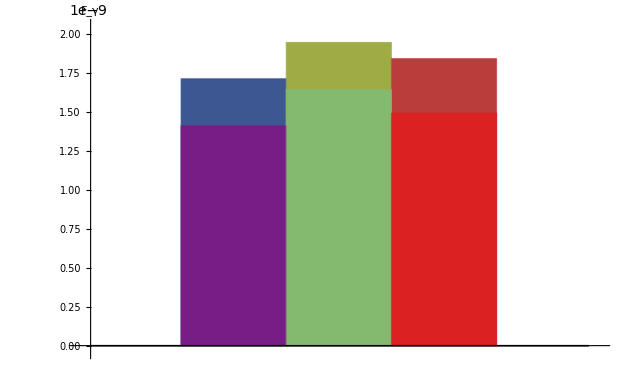

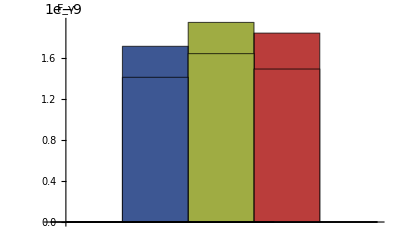

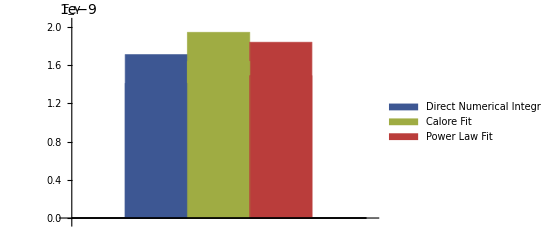

```mathematica
(*REFERENCE 42 Fitting; this is the only reference where the reference paper does not simply trust the results of the reference*)
AIC={{-17.735173357664234,861.9931321988181},{-17.611724452554746,946.1719920451017},{-17.488275547445255,1093.595913336047},{-17.364826642335768,1246.6036979832309},{-17.24137773722628,1421.0191907949613},{-17.11792883211679,1609.6715456082065},{-16.9944799270073,1798.2883582829563},{-16.87103102189781,1996.3982946401766},{-16.747582116788323,2227.524114546515},{-16.62413321167883,2510.5702120151554},{-16.500684306569344,2953.3501849328604},{-16.377235401459856,3558.340554456744},{-16.253786496350365,4201.753871530058},{-16.130337591240878,4961.5081318750335},{-16.006888686131386,5684.242616636822},{-15.883439781021899,6302.511142187449},{-15.75999087591241,7175.271070886809},{-15.63654197080292,7875.979829777422},{-15.513093065693432,8623.373452056408},{-15.389644160583943,9429.810212192182},{-15.266195255474454,9805.168094822222},{-15.142746350364964,10131.480816454849},{-15.019297445255475,10234.05295131953},{-14.895848540145986,10169.824336545023},{-14.772399635036498,10017.315482652992},{-14.648950729927009,9585.43647991601},{-14.52550182481752,8932.823660868668},{-14.40205291970803,8097.204572430072},{-14.27860401459854,7211.501186915323},{-14.155155109489053,6398.4638705008765},{-14.031706204379564,5634.36158983417},{-13.913868613138687,4677.583167431803},{-13.781355277933747,3430.251833784642},{-13.65013686131387,2851.0404488270487},{-13.52668795620438,2235.0161142459992},{-13.396692518248177,1656.4484113770377},{-13.25734489051095,1204.7184622134164},{-13.14231295620438,897.1829285093002},{-13.055337591240876,684.2554323172905},{-12.963686131386863,514.2744259173232},{-12.879856502986067,353.3484599472582},{-12.800958029197082,254.02907040285777},{-12.71865875912409,195.36507726463154},{-12.647582116788323,134.792047506197},{-12.56154197080292,102.7935152385697},{-12.463032238442823,75.3251282910665},{-12.348312043795621,52.796971631975495},{-12.224863138686134,41.3833393505801},{-12.133679288321169,26.717931426867867},{-12.0827098540146,20.016830239781562},{-12.015,14.932495306500163},{-11.969236618004867,11.243834311418269},{-11.910629562043797,8.185178767528205},{-11.864336222627738,6.008798720500609},{-11.804014598540148,4.366525036351495}};

GEC={{8.083433445459244*10^+30,0.12253130147539532},{8.708543449362236*10^+30,0.13120980294479181},{9.778882018845654*10^+30,0.14915068549207283},{1.0534962342100723*10^+31,0.15879107200416184},{1.182958004450293*10^+31,0.17919960117530562},{1.274422786480575*10^+31,0.19086124487093348},{1.442875244144245*10^+31,0.21374208459054858},{1.5544023208669335*10^+31,0.2255165079460105},{1.7598295753907183*10^+31,0.2505461957973092},{1.895835494082*10^+31,0.26314635557326405},{2.1463507381170347*10^+31,0.29030115617536795},{2.312204934429997*10^+31,0.3035774473038215},{2.639389573858031*10^+31,0.3317551885024173},{2.8433215790630617*10^+31,0.3458512223160999},{3.2455857120569807*10^+31,0.3742141969991605},{3.496297086310092*10^+31,0.38733684453364325},{3.9908669293134435*10^+31,0.41573057880073994},{4.299092873321075*10^+31,0.42790962349711503},{4.907070725161617*10^+31,0.45323020788207996},{5.286024480456222*10^+31,0.46525352257036423},{6.08343180431545*10^+31,0.48663588298317506},{6.553126815658976*10^+31,0.49614295089593924},{7.479543182356586*10^+31,0.5157434952031216},{8.0901640038769625*10^+31,0.5201265839039854},{9.271578209277244*10^+31,0.5282712310335946},{9.987315483083716*10^+31,0.5360323030534359},{1.1493105649474118*10^+32,0.5438558068271622},{1.237997314257171*10^+32,0.5449181034051269},{1.4246009368216386*10^+32,0.5446884079339263},{1.5345227310256288*10^+32,0.5445668436495613},{1.7657589951314505*10^+32,0.5361141449254088},{1.9019759597646335*10^+32,0.5325643473557506},{2.18852007818422*10^+32,0.5178232748067827},{2.3573059279139305*10^+32,0.510256569610932},{2.6900808976760716*10^+32,0.4915428793895911},{2.909522404287703*10^+32,0.4832144999977357},{3.3338966767019156*10^+32,0.45986934031230337},{3.590913633811528*10^+32,0.4475534419099194},{4.0976339579227574*10^+32,0.42221478904009097},{4.4317851040784164*10^+32,0.41064701647990925},{5.036168255519862*10^+32,0.38234129201852013},{5.446764575770642*10^+32,0.369247124389946},{6.1894055906983956*10^+32,0.34001567164019797},{6.693948378668357*10^+32,0.3267683194887266},{7.606479540105318*10^+32,0.29823969204260875},{8.1925303878752*10^+32,0.2850105165416067},{9.270860200771083*10^+32,0.2585865315577682},{1.0026348590514926*10^+33,0.24591345591160077},{1.1299005155011672*10^+33,0.2206585360526757},{1.2169242645603136*10^+33,0.20859032321074683},{1.3770349387710246*10^+33,0.18544910350269378},{1.4830930793909292*10^+33,0.1753247120549692},{1.664400715484684*10^+33,0.1550728990614128},{1.7925417431882306*10^+33,0.1448713701477331},{2.0116502187031733*10^+33,0.12734357648024136},{2.166522598625655*10^+33,0.11889234002963782},{2.4312817704063279*10^+33,0.10336686865932718},{2.607619450260593*10^+33,0.09570196995362742},{2.914241684798721*10^+33,0.08342150839478185},{3.125626312661483*10^+33,0.07743180086417273},{3.493056070136472*10^+33,0.0666449887788865},{3.7795229901554397*10^+33,0.060474318790966},{4.186669295000096*10^+33,0.05236203680723728},{4.551270273570114*10^+33,0.04672275712247589},{5.017919381526731*10^+33,0.040813397641842664},{5.480514580574942*10^+33,0.035852365438854394},{6.014008179425021*10^+33,0.03135399932824517},{6.59934474796077*10^+33,0.027261494780642034},{7.207619721263924*10^+33,0.023792031047086964},{7.983661759451904*10^+33,0.020169858764122844},{8.496851043532927*10^+33,0.018263477791800247}};

(*AICwErrors={{-17.778941605839417,623.4497391611966},{-17.75836678832117,889.623901060933},{-17.751824817518248,1110.1544690790593},{-17.651003649635037,678.1004211168172},{-17.635036496350367,1193.1150284921346},{-17.63491788321168,967.6367989722481},{-17.521943430656936,773.8191545838605},{-17.509224452554744,1110.838906906629},{-17.503649635036496,1329.3234711599416},{-17.39951476443265,911.0974655235195},{-17.37765250260688,1320.4564933544787},{-17.37226277372263,1650.1650571873286},{-17.272551703163018,1037.651590882174},{-17.253348540145986,1509.113698862136},{-17.24087591240876,1838.5512623869934},{-17.138971259124087,1152.8655401681463},{-17.129852874087593,1692.7362216498673},{-17.124087591240876,2048.444020615976},{-17.015678223844283,1281.8580671260631},{-17.00729927007299,2366.0390561145355},{-17.006403968978102,1894.4179158084116},{-16.883573958780595,2044.4126447223405},{-16.877443952033367,1400.7167568416226},{-16.875912408759127,2542.8504180966893},{-16.759124087591243,2833.147402976567},{-16.75824361313869,2137.2664375154045},{-16.745337591240876,1605.6230113897973},{-16.638161496350364,2367.3982507447517},{-16.627737226277375,3156.58528314097},{-16.60168795620438,1882.864439260431},{-16.525547445255476,3516.947490721351},{-16.52425182481752,2747.983491916943},{-16.51094890510949,2048.444020615976},{-16.432413321167886,3447.4064485388512},{-16.423357664233578,4211.270572221615},{-16.412306113138687,2458.174866107265},{-16.325330748175183,3986.8621328740855},{-16.32116788321168,4864.19474950843},{-16.284648722627736,2877.6391678058503},{-16.204379562043798,5824.494184289978},{-16.204379562043798,3156.58528314097},{-16.20301746611053,4213.74626574766},{-16.109618893879844,5286.73018723015},{-16.1021897810219,6489.430307986684},{-16.07703010948905,3822.5143943460716},{-15.99698636753972,5926.360642663167},{-15.985401459854016,7495.565124602608},{-15.949172314911367,4326.773961551464},{-15.87119691439947,6189.7849171152},{-15.854014598540147,8351.274111713074},{-15.854014598540147,4692.037801362983},{-15.754049484757408,7449.216641468032},{-15.751824817518251,9304.672580330143},{-15.731132690302399,5242.259312819943},{-15.635036496350367,10366.912960708527},{-15.634561507084587,8138.813164657029},{-15.607683785192911,5674.027077259201},{-15.518248175182483,11141.620375362701},{-15.509975669099756,8674.31518198032},{-15.475684306569343,6297.222826485339},{-15.391624624302276,9694.344685696668},{-15.386861313868614,11974.22077904795},{-15.354373044838376,6833.885980924348},{-15.266195255474454,10146.694376874211},{-15.255474452554747,12413.570458869755},{-15.252821949947863,7053.698463990942},{-15.142746350364964,10410.650592133758},{-15.138686131386862,12413.570458869755},{-15.128455748175183,7393.086746999728},{-15.017801094890512,10854.643016854596},{-15.007299270072995,13341.222221093207},{-15.004320907194995,7554.517654225282},{-14.892341468978103,10497.527611398444},{-14.890510948905112,13341.222221093207},{-14.880872002085505,7421.177804803303},{-14.768892563868615,10431.700166733232},{-14.765408302919708,7427.298666362505},{-14.759124087591243,12869.040447872536},{-14.645443658759126,9968.50570198903},{-14.64233576642336,12869.040447872536},{-14.636815693430655,7009.896655691183},{-14.524005474452556,9346.537577652642},{-14.516245023224949,6523.599677780638},{-14.51094890510949,11344.1793215166},{-14.380748175182482,5905.794956861959},{-14.38035583941606,8393.548769035522},{-14.379562043795621,9999.999999999989},{-14.258748596294218,7303.976169018824},{-14.257922749391728,5067.968909180209},{-14.248175182481752,8975.355166572359},{-14.148403284671534,4527.284684151354},{-14.13448253388947,6473.95679224987},{-14.13138686131387,7770.587123807769},{-14.032953163017032,4030.176572010303},{-14.032569483436273,5764.440638507576},{-14.029197080291974,7230.276894396076},{-13.916419210351693,4734.034723982487},{-13.912408759124089,5824.494184289978},{-13.903768248175185,3417.087527847205},{-13.791541970802921,2721.3587537584635},{-13.784808394160585,3761.1716248214343},{-13.781021897810222,4692.037801362983},{-13.647933043234142,2135.825675137287},{-13.635036496350367,3779.76490882236},{-13.632501303441085,2869.093702930154},{-13.514533368091767,1562.917977060525},{-13.507303417385534,2212.916968770989},{-13.503649635036497,2937.0992531515503},{-13.369045191069132,1140.1734148079677},{-13.36185561131387,1632.5529061177672},{-13.357664233576644,2048.444020615976},{-13.247525091240878,1460.0382163133263},{-13.246113968148645,839.8857153483657},{-13.240875912408761,1150.8874753884218},{-13.080291970802921,961.1376778706134},{-13.080291970802921,720.4270058188521},{-13.080291970802921,520.8886734271005},{-12.95492460622359,452.486983175274},{-12.948905109489054,326.06338620149677},{-12.943704379562043,581.2896705117141},{-12.86848083941606,321.35057782570664},{-12.86131386861314,227.40892841451094},{-12.86131386861314,419.61229055973547},{-12.735492700729928,249.24129424377816},{-12.73321167883212,204.3534317880945},{-12.729927007299272,142.3523471213787},{-12.585051703163018,98.21969791630141},{-12.583941605839417,137.31411429892975},{-12.583941605839417,176.71008909767232},{-12.48175182481752,57.82668886977605},{-12.48031152241919,80.22496527444493},{-12.478695255474452,110.37868219618754},{-12.385520072992703,54.31916079006106},{-12.384523266423358,37.94263980618774},{-12.382563868613138,75.86305379224967},{-12.280976277372265,48.443545341912554},{-12.277372262773724,59.94842503189396},{-12.277372262773724,32.48905573870442},{-12.208652676399028,28.586719908819415},{-12.205976277372264,42.496346165302455},{-12.204379562043798,51.901507071311734},{-12.129489051094891,19.220672715542012},{-12.1280370177268,26.98334592282258},{-12.124087591240878,34.91692529556037},{-12.065693430656937,10.44189550341823},{-12.05839416058394,17.293053078863938},{-12.056276068821687,23.77293955927567},{-11.987241484184917,7.232624177988733},{-11.985401459854018,11.845473504731306},{-11.985401459854018,15.803309434069243},{-11.927007299270075,4.477310508156859},{-11.927007299270075,7.687037477405681},{-11.91240875912409,11.021825252050114},{-11.824817518248178,6.899389153846851},{-11.824817518248178,4.988449398450599},{-11.824817518248178,2.703490716724295}};*)
AICwErrors={{10^-17.7789,623.45},{10^-17.7584,889.624},{10^-17.7518,1110.15},{10^-17.651,678.1},{10^-17.6349,967.637},{10^-17.635,1193.12},{10^-17.5219,773.819},{10^-17.5092,1110.84},{10^-17.5036,1329.32},{10^-17.3995,911.097},{10^-17.3777,1320.46},{10^-17.3723,1650.17},{10^-17.2726,1037.65},{10^-17.2533,1509.11},{10^-17.2409,1838.55},{10^-17.139,1152.87},{10^-17.1299,1692.74},{10^-17.1241,2048.44},{10^-17.0157,1281.86},{10^-17.0064,1894.42},{10^-17.0073,2366.04},{10^-16.8774,1400.72},{10^-16.8836,2044.41},{10^-16.8759,2542.85},{10^-16.7453,1605.62},{10^-16.7582,2137.27},{10^-16.7591,2833.15},{10^-16.6017,1882.86},{10^-16.6382,2367.4},{10^-16.6277,3156.59},{10^-16.5109,2048.44},{10^-16.5243,2747.98},{10^-16.5255,3516.95},{10^-16.4123,2458.17},{10^-16.4324,3447.41},{10^-16.4234,4211.27},{10^-16.2846,2877.64},{10^-16.3253,3986.86},{10^-16.3212,4864.19},{10^-16.2044,3156.59},{10^-16.203,4213.75},{10^-16.2044,5824.49},{10^-16.077,3822.51},{10^-16.1096,5286.73},{10^-16.1022,6489.43},{10^-15.9492,4326.77},{10^-15.997,5926.36},{10^-15.9854,7495.57},{10^-15.854,4692.04},{10^-15.8712,6189.78},{10^-15.854,8351.27},{10^-15.7311,5242.26},{10^-15.754,7449.22},{10^-15.7518,9304.67},{10^-15.6077,5674.03},{10^-15.6346,8138.81},{10^-15.635,10366.9},{10^-15.4757,6297.22},{10^-15.51,8674.32},{10^-15.5182,11141.6},{10^-15.3544,6833.89},{10^-15.3916,9694.34},{10^-15.3869,11974.2},{10^-15.2528,7053.7},{10^-15.2662,10146.7},{10^-15.2555,12413.6},{10^-15.1285,7393.09},{10^-15.1427,10410.7},{10^-15.1387,12413.6},{10^-15.0043,7554.52},{10^-15.0178,10854.6},{10^-15.0073,13341.2},{10^-14.8809,7421.18},{10^-14.8923,10497.5},{10^-14.8905,13341.2},{10^-14.7654,7427.3},{10^-14.7689,10431.7},{10^-14.7591,12869.},{10^-14.6368,7009.9},{10^-14.6454,9968.51},{10^-14.6423,12869.},{10^-14.5162,6523.6},{10^-14.524,9346.54},{10^-14.5109,11344.2},{10^-14.3807,5905.79},{10^-14.3804,8393.55},{10^-14.3796,10000.},{10^-14.2579,5067.97},{10^-14.2587,7303.98},{10^-14.2482,8975.36},{10^-14.1484,4527.28},{10^-14.1345,6473.96},{10^-14.1314,7770.59},{10^-14.033,4030.18},{10^-14.0326,5764.44},{10^-14.0292,7230.28},{10^-13.9038,3417.09},{10^-13.9164,4734.03},{10^-13.9124,5824.49},{10^-13.7915,2721.36},{10^-13.7848,3761.17},{10^-13.781,4692.04},{10^-13.6479,2135.83},{10^-13.6325,2869.09},{10^-13.635,3779.76},{10^-13.5145,1562.92},{10^-13.5073,2212.92},{10^-13.5036,2937.1},{10^-13.369,1140.17},{10^-13.3619,1632.55},{10^-13.3577,2048.44},{10^-13.2461,839.886},{10^-13.2409,1150.89},{10^-13.2475,1460.04},{10^-13.0803,520.889},{10^-13.0803,720.427},{10^-13.0803,961.138},{10^-12.9489,326.063},{10^-12.9549,452.487},{10^-12.9437,581.29},{10^-12.8613,227.409},{10^-12.8685,321.351},{10^-12.8613,419.612},{10^-12.7299,142.352},{10^-12.7332,204.353},{10^-12.7355,249.241},{10^-12.5851,98.2197},{10^-12.5839,137.314},{10^-12.5839,176.71},{10^-12.4818,57.8267},{10^-12.4803,80.225},{10^-12.4787,110.379},{10^-12.3845,37.9426},{10^-12.3855,54.3192},{10^-12.3826,75.8631},{10^-12.2774,32.4891},{10^-12.281,48.4435},{10^-12.2774,59.9484},{10^-12.2087,28.5867},{10^-12.206,42.4963},{10^-12.2044,51.9015},{10^-12.1295,19.2207},{10^-12.128,26.9833},{10^-12.1241,34.9169},{10^-12.0657,10.4419},{10^-12.0584,17.2931},{10^-12.0563,23.7729},{10^-11.9872,7.23262},{10^-11.9854,11.8455},{10^-11.9854,15.8033},{10^-11.927,4.47731},{10^-11.927,7.68704},{10^-11.9124,11.0218},{10^-11.8248,2.70349},{10^-11.8248,4.98845},{10^-11.8248,6.89939}};
AIC={};
AICHErr={};
AICLErr={};
For[i=1,i<53,i++,
If[AICwErrors[[i*3-2]].{0,1}>AICwErrors[[i*3-1]].{0,1},AICwErrors[[{i*3-2,i*3-1}]]=AICwErrors[[{i*3-1,i*3-2}]] ];
If[AICwErrors[[i*3-1]].{0,1}>AICwErrors[[i*3]].{0,1},AICwErrors[[{i*3-1,i*3}]]=AICwErrors[[{i*3,i*3-1}]] ];
If[AICwErrors[[i*3-2]].{0,1}>AICwErrors[[i*3-1]].{0,1},AICwErrors[[{i*3-2,i*3-1}]]=AICwErrors[[{i*3-1,i*3-2}]] ];
]

For[i=1,i<53,i++,AppendTo[AICHErr,AICwErrors[[i*3]]]]
For[i=1,i<53,i++,AppendTo[AIC,AICwErrors[[i*3-1]]]]
For[i=1,i<53,i++,AppendTo[AICLErr,AICwErrors[[i*3-2]]]]
```

```mathematica
AICH=AICHErr.{0,1}-AIC.{0,1};
AICL=AICLErr.{0,1}-AIC.{0,1};

For[i=1,i<53,i++,
AppendTo[AIC[[i]],0];
AppendTo[AIC[[i]],0];
AppendTo[AIC[[i]],AICL[[i]]];
AppendTo[AIC[[i]],AICH[[i]]]
]


(*AIC.DiagonalMatrix[{4 Pi R0^2,1/( 5*10^33), 1, 1,1/( 5 10^33),1/( 5*10^33)}]//MatrixForm*)
```

```mathematica
(*Converting Flux to Luminosity*)
Clear[kpc,cm,R0,rc,ρ,rLat];
R0=8.5 kpc; (*If we assume all MSPs are in the galactic center*)
rc=20 kpc;
kpc=3.086 10^21 cm;
cm=1;
1/(4 Pi R0^2)

ρ[r_]:=(r/rc)^(-2γ)(1+r/rc)^(-6+2 γ);
γ=1;
rLat[s_,b_,l_]=Sqrt[R0^2+s^2-2 R0 s Cos[b] Cos[l]];
NIntegrate[ρ[rLat[s,b-90 Degree,l]] Cos[b] UnitStep[Abs[b]-2 Degree],{s,0,Infinity},{b,-20 Degree,20 Degree},{l,0,20 Degree},Method->"GlobalAdaptive",WorkingPrecision->10]/(4 Pi NIntegrate[s^2 ρ[rLat[s,b-90 Degree,l]] Cos[b] UnitStep[Abs[b]-2 Degree],{s,0,Infinity},{b,-20 Degree,20 Degree},{l,0,20 Degree},Method->"GlobalAdaptive",WorkingPrecision->10])
(*NIntegrate[ρ[rLat[s,b,l]] Sin[b],{s,0,Infinity},{b,2 Degree,20 Degree},{l,0,20 Degree},Method->"GlobalAdaptive",WorkingPrecision->10]/(4 Pi NIntegrate[s^2 ρ[rLat[s,b,l]] Sin[b],{s,0,Infinity},{b,2 Degree,20 Degree},{l,0,20 Degree},Method->"GlobalAdaptive",WorkingPrecision->10]) WRONG PREVIOUS ATTEMPT*)
```

1.15654×10^-46

1.11587398×10^-46

```mathematica
(*Here we Get AIC Datas and we Normalize them*)
Clear[Normalization];
Normalization=NIntegrate[Interpolation[AIC.DiagonalMatrix[{4 Pi R0^2,1}]][x],{x,1.6 10^28,10^34},Method->"GlobalAdaptive",MinRecursion->5];
NormalizationGEC=NIntegrate[Interpolation[GEC][x],{x,1.6 10^31,10^34},Method->"GlobalAdaptive",MinRecursion->5];
```

InterpolatingFunction::dmvali: The integration endpoint 10000000000000000000000000000000000 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
AICH=AICHErr.{0,1}-AIC.{0,1};
AICL=AICLErr.{0,1}-AIC.{0,1};

For[i=1,i<53,i++,
AppendTo[AIC[[i]],0];
AppendTo[AIC[[i]],0];
AppendTo[AIC[[i]],AICL[[i]]];
AppendTo[AIC[[i]],AICH[[i]]]
]


AIC.DiagonalMatrix[{4 Pi R0^2,1/Normalization, 1, 1,1/Normalization,1/Normalization}]//MatrixForm
```

(0.+2.19185×10^-17 R0^2 | 2.65686×10^35 | 0. | 0. | -7.94928×10^34 | 6.58601×10^34
0.+2.91279×10^-17 R0^2 | 2.88985×10^35 | 0. | 0. | -8.64702×10^34 | 6.73405×10^34
0.+3.89054×10^-17 R0^2 | 3.31752×10^35 | 0. | 0. | -1.00651×10^35 | 6.5249×10^34
0.+5.26635×10^-17 R0^2 | 3.94355×10^35 | 0. | 0. | -1.22256×10^35 | 9.84679×10^34
0.+7.0131×10^-17 R0^2 | 4.50696×10^35 | 0. | 0. | -1.40801×10^35 | 9.83872×10^34
0.+9.31772×10^-17 R0^2 | 5.05537×10^35 | 0. | 0. | -1.61232×10^35 | 1.0623×10^35
0.+1.23825×10^-16 R0^2 | 5.65768×10^35 | 0. | 0. | -1.82941×10^35 | 1.40849×10^35
0.+1.6429×10^-16 R0^2 | 6.10563×10^35 | 0. | 0. | -1.92238×10^35 | 1.48859×10^35
0.+2.19285×10^-16 R0^2 | 6.38295×10^35 | 0. | 0. | -1.58777×10^35 | 2.07824×10^35
0.+2.89075×10^-16 R0^2 | 7.07024×10^35 | 0. | 0. | -1.44708×10^35 | 2.35692×10^35
0.+3.75759×10^-16 R0^2 | 8.20684×10^35 | 0. | 0. | -2.08918×10^35 | 2.29653×10^35
0.+4.64312×10^-16 R0^2 | 1.02957×10^36 | 0. | 0. | -2.95436×10^35 | 2.28127×10^35
0.+5.94169×10^-16 R0^2 | 1.19068×10^36 | 0. | 0. | -3.31268×10^35 | 2.62015×10^35
0.+7.87426×10^-16 R0^2 | 1.25844×10^36 | 0. | 0. | -3.15721×10^35 | 4.81047×10^35
0.+9.7636×10^-16 R0^2 | 1.57888×10^36 | 0. | 0. | -4.37289×10^35 | 3.59186×10^35
0.+1.26535×10^-15 R0^2 | 1.76991×10^36 | 0. | 0. | -4.77717×10^35 | 4.68644×10^35
0.+1.69048×10^-15 R0^2 | 1.84858×10^36 | 0. | 0. | -4.473×10^35 | 6.45529×10^35
0.+2.21416×10^-15 R0^2 | 2.22471×10^36 | 0. | 0. | -6.59108×10^35 | 5.5413×10^35
0.+2.91481×10^-15 R0^2 | 2.43065×10^36 | 0. | 0. | -7.36106×10^35 | 6.65419×10^35
0.+3.88338×10^-15 R0^2 | 2.59058×10^36 | 0. | 0. | -7.09921×10^35 | 7.36853×10^35
0.+5.10047×10^-15 R0^2 | 2.89521×10^36 | 0. | 0. | -8.54273×10^35 | 6.8088×10^35
0.+6.80785×10^-15 R0^2 | 3.03031×10^36 | 0. | 0. | -9.23724×10^35 | 6.77009×10^35
0.+9.04711×10^-15 R0^2 | 3.10915×10^36 | 0. | 0. | -9.01209×10^35 | 5.98166×10^35
0.+1.20617×10^-14 R0^2 | 3.24173×10^36 | 0. | 0. | -9.85569×10^35 | 7.42623×10^35
0.+1.61031×10^-14 R0^2 | 3.13508×10^36 | 0. | 0. | -9.18743×10^35 | 8.49271×10^35
0.+2.13949×10^-14 R0^2 | 3.11543×10^36 | 0. | 0. | -8.97264×10^35 | 7.27899×10^35
0.+2.84322×10^-14 R0^2 | 2.97709×10^36 | 0. | 0. | -8.83589×10^35 | 8.66231×10^35
0.+3.76019×10^-14 R0^2 | 2.79134×10^36 | 0. | 0. | -8.43071×10^35 | 5.96601×10^35
0.+5.23371×10^-14 R0^2 | 2.50673×10^36 | 0. | 0. | -7.42969×10^35 | 4.79766×10^35
0.+6.92644×10^-14 R0^2 | 2.18133×10^36 | 0. | 0. | -6.67784×10^35 | 4.99157×10^35
0.+9.21955×10^-14 R0^2 | 1.93345×10^36 | 0. | 0. | -5.81376×10^35 | 3.87238×10^35
0.+1.16576×10^-13 R0^2 | 1.72155×10^36 | 0. | 0. | -5.17937×10^35 | 4.37773×10^35
0.+1.52339×10^-13 R0^2 | 1.41382×10^36 | 0. | 0. | -3.93304×10^35 | 3.25666×10^35
0.+2.06258×10^-13 R0^2 | 1.12327×10^36 | 0. | 0. | -3.10539×10^35 | 2.78004×10^35
0.+2.92894×10^-13 R0^2 | 8.56853×10^35 | 0. | 0. | -2.18988×10^35 | 2.71972×10^35
0.+3.9076×10^-13 R0^2 | 6.60888×10^35 | 0. | 0. | -1.94122×10^35 | 2.16276×10^35
0.+5.46147×10^-13 R0^2 | 4.87561×10^35 | 0. | 0. | -1.47049×10^35 | 1.24206×10^35
0.+7.21622×10^-13 R0^2 | 3.43713×10^35 | 0. | 0. | -9.28813×10^34 | 9.23276×10^34
0.+1.0445×10^-12 R0^2 | 2.15155×10^35 | 0. | 0. | -5.9592×10^34 | 7.18883×10^34
0.+1.39415×10^-12 R0^2 | 1.35135×10^35 | 0. | 0. | -3.77565×10^34 | 3.8467×10^34
0.+1.70102×10^-12 R0^2 | 9.59714×10^34 | 0. | 0. | -2.80558×10^34 | 2.93456×10^34
0.+2.32279×10^-12 R0^2 | 6.103×10^34 | 0. | 0. | -1.85166×10^34 | 1.34058×10^34
0.+3.27574×10^-12 R0^2 | 4.10088×10^34 | 0. | 0. | -1.16755×10^34 | 1.17656×10^34
0.+4.15824×10^-12 R0^2 | 2.39592×10^34 | 0. | 0. | -6.68925×10^33 | 9.00549×10^33
0.+5.17261×10^-12 R0^2 | 1.62224×10^34 | 0. | 0. | -4.89087×10^33 | 6.43408×10^33
0.+6.57976×10^-12 R0^2 | 1.44676×10^34 | 0. | 0. | -4.76478×10^33 | 3.43594×10^33
0.+7.82006×10^-12 R0^2 | 1.26915×10^34 | 0. | 0. | -4.1541×10^33 | 2.80886×10^33
0.+9.35858×10^-12 R0^2 | 8.05856×10^33 | 0. | 0. | -2.3183×10^33 | 2.36937×10^33
0.+1.09852×10^-11 R0^2 | 5.16458×10^33 | 0. | 0. | -2.04611×10^33 | 1.93519×10^33
0.+1.2996×10^-11 R0^2 | 3.53766×10^33 | 0. | 0. | -1.37764×10^33 | 1.182×10^33
0.+1.48665×10^-11 R0^2 | 2.29573×10^33 | 0. | 0. | -9.58586×10^32 | 9.95926×10^32
0.+1.88109×10^-11 R0^2 | 1.4898×10^33 | 0. | 0. | -6.82403×10^32 | 5.70702×10^32)

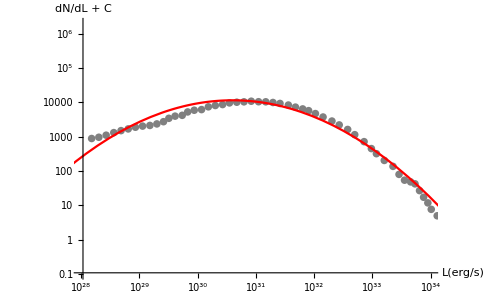

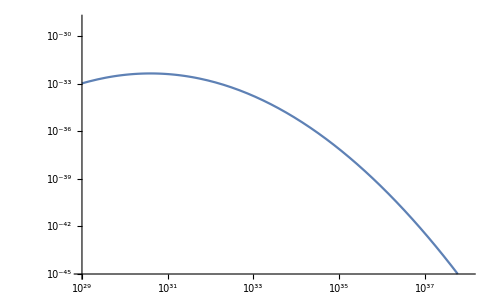

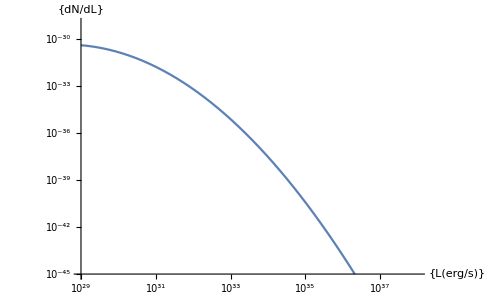

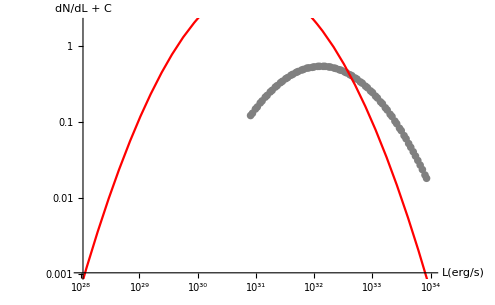

```mathematica
(*Using Log Normal and the values extracted from page 15 we DON'T simulate the expected curve*)
Clear[L0,σ];
F[x_]:=  E^(-(Log10[x]-Log10[L0])^2/(2σ^2))   Log10[E]/(σ Sqrt[2 Pi] x);

(*MY ROOT VALUES*)
(*L0=3.65649 10^32; 
σ=0.882369;*)
L0=4.3 10^32;  (*THERE WAS A MISTAKE HERE*)
σ=0.94;


Show[ListLogLogPlot[AIC.DiagonalMatrix[{4 Pi R0^2,1}],PlotRange->{{10^28,10^34},{10^-1,2 10^6}},PlotStyle->{Gray},AxesLabel->{"L(erg/s)","dN/dL + C"},PlotLegends->Placed[{"AIC points"},{Right,Top}]],
	LogLogPlot[Normalization  F[x],{x,10^27,10^36},PlotLegends->Placed[{"Log Normal Fit"},{Right,Top}],PlotStyle->{Red}]]
LogLogPlot[F[x],{x,10^29,10^38},PlotRange->{{10^29,10^38},{10^-45,10^-29}}]
L0=4.3 10^30; 
σ=0.94;
LogLogPlot[F[x],{x,10^29,10^38},PlotRange->{{10^29,10^38},{10^-45,10^-29}},AxesLabel->{{"L(erg/s)"},{"dN/dL"}}]

L0=1.3 10^32;
σ=0.7;
Show[ListLogLogPlot[GEC,PlotRange->{{10^28,10^34},{10^-3,2 10^0}},PlotStyle->{Gray},AxesLabel->{"L(erg/s)","dN/dL + C"},PlotLegends->Placed[{"AIC points"},{Right,Top}]],
	LogLogPlot[NormalizationGEC  F[x],{x,10^27,10^36},PlotLegends->Placed[{"Log Normal Fit"},{Right,Top}],PlotStyle->{Red}]]

(*F1=NonlinearModelFit[AIC,{F[x],L0>0,σ>0},{L0,σ},x,Tolerance->10^(-12)];
F1["ParameterTable"]*)
```

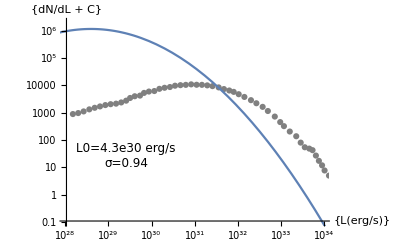

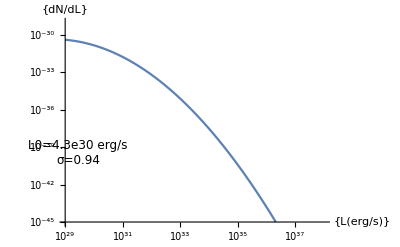

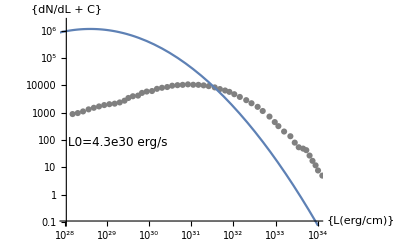

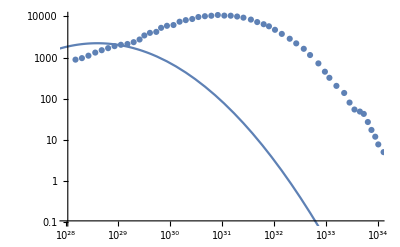

```mathematica
0
```

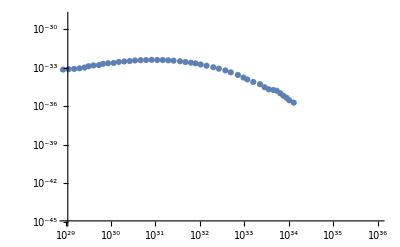

InterpolatingFunction::dmvali: The integration endpoint 10000000000000000000000000000 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

2.58801×10^36

```mathematica
ListLogLogPlot[AIC.DiagonalMatrix[{4 Pi R0^2,1/Normalization}],PlotRange->{{10^29,10^36},{10^-45,10^-29}}]
```

```mathematica
(*Datas are given as L^2 dn/dL for GLC, so it's time to untangle them; here's GLC*)
Clear[GLC,GLCsq,Normalization,GLCX,GLCY,GLCYwLsq];
(*GLCLsq={{1.2116702439129589*10^+32,0.001274252485481965},{1.3270941676674236*10^+32,0.001642456990709944},{1.480260613288642*10^+32,0.002323445007501771},{1.681378685900935*10^+32,0.00334300291631878},{1.8754303293671374*10^+32,0.004715759726664859},{2.1302285348601793*10^+32,0.00674697452796172},{2.4196322768487935*10^+32,0.00959885686490778},{2.7483465564562325*10^+32,0.013617785296689331},{3.1217101372571453*10^+32,0.01926504250245564},{3.545761105214029*10^+32,0.02694880722994247},{4.027424563704443*10^+32,0.037803551518168214},{4.658360893862037*10^+32,0.05348366847491759},{5.3393900720964524*10^+32,0.07467713724072958},{6.1199872387011044*10^+32,0.10436670192910824},{7.143165442462366*10^+32,0.1445729383931448},{8.262120898925126*10^+32,0.2018673255195385},{9.6434500467495*10^+32,0.28016038765293466},{1.1255612725861142*10^+33,0.38446208564486517},{1.325709948826527*10^+33,0.5281054872858871},{1.5614399071866782*10^+33,0.7203260935023817},{1.8390638415959168*10^+33,0.9687689787558879},{2.2057420174364658*10^+33,1.3091081522872647},{2.6490217565740215*10^+33,1.8159065371112502},{3.221392788991953*10^+33,2.4074969424886774},{3.992747937706935*10^+33,3.278811587027012},{4.8763992267113937*10^+33,4.253312559856084},{5.868544030498771*10^+33,5.3209280477025995},{6.995564556133694*10^+33,6.502748201196506},{8.621366128755865*10^+33,8.072008859442027},{1.0819547957385983*10^+34,9.88834462027711},{1.3455279676447413*10^+34,11.88367691345069},{1.703936907119658*10^+34,13.997937358919888},{2.1774485122118982*10^+34,16.106239504034846},{2.78247534088565*10^+34,17.993136313489448},{3.5879416394094564*10^+34,19.4778417476301},{4.626461573421146*10^+34,20.499346413749567},{6.019770413457649*10^+34,20.723995323368854},{7.761733799211586*10^+34,20.4027114582931},{1.009872816574068*10^+35,19.385442081296453},{1.3020299479813858*10^+35,17.864737383691864},{1.6484638362403964*10^+35,15.972899973200622},{2.1060521139338813*10^+35,13.861825073451179},{2.666296194141682*10^+35,11.770017737499277},{3.345008778082658*10^+35,9.778086657012114},{4.158485798371705*10^+35,7.93721416747431},{5.169731110018129*10^+35,6.3527962306915695},{6.368718010994018*10^+35,4.998284164702814},{7.92731117433163*10^+35,3.7699807292192},{9.462814228116825*10^+35,3.0847871052739553}};*)
GLCLsq={{1.2116723780784525*10^+32,0.0012309356206005075},{1.4016237532217098*10^+32,0.0019423952172281482},{1.7437116459132406*10^+32,0.00358842738683154},{2.0170600043069985*10^+32,0.005630662243801666},{2.5093465491888282*10^+32,0.0103632205736497},{2.9558715891636763*10^+32,0.016093534658731222},{3.677096944247308*10^+32,0.0278924038320226},{4.410924185553293*10^+32,0.045098961556231366},{5.587649849370126*10^+32,0.07721235190411165},{6.8255656748417*10^+32,0.12495759411694435},{8.646208242857274*10^+32,0.20682413498389654},{1.0755102010327469*10^+33,0.3300252555531316},{1.3747696473833458*10^+33,0.5260978032507132},{1.773340651891962*10^+33,0.848948300866318},{2.3293448074283355*10^+33,1.350722344768379},{3.004495901835347*10^+33,2.0409536072743117},{4.018684287817541*10^+33,3.127464943328177},{5.302232217786205*10^+33,4.49286379594326},{7.523017307323928*10^+33,6.811672566914479},{9.790907851345609*10^+33,9.013829610765578},{1.4417405991823631*10^+34,12.516489840970749},{2.0249491028885715*10^+34,15.723641437788363},{2.93844353238617*10^+34,18.916518234051324},{4.302655969515018*10^+34,21.202668385490547},{6.357306867345569*10^+34,22.215577121877068},{9.392535363395133*10^+34,21.65030112390506},{1.3750664440130876*10^+35,19.64503348634849},{2.012971562837042*10^+35,16.579860338948013},{2.8675129810380204*10^+35,13.284701261320045},{4.047732431267051*10^+35,10.112168609604181},{5.661840076271543*10^+35,7.327103165203622},{7.776901446366435*10^+35,5.137584827294065}};
GLCX=GLCLsq.{1,0};
GLCYwLsq=GLCLsq.{0,1};
GLCY={};
For [i=1, i<33,i++,
AppendTo[GLCY,GLCYwLsq[[i]]/(GLCX[[i]])^2];
]
GLC={};
For [i=1, i<33,i++,
AppendTo[GLC,{GLCX[[i]],GLCY[[i]]}];
]
(*Now we normalize it*)
Normalization=NIntegrate[Interpolation[GLC][x],{x,1.3 10^32,7.5 10^35},Method->"GlobalAdaptive",MinRecursion->5];
GLC.DiagonalMatrix[{1,1/Normalization}] //MatrixForm
```

(1.21167×10^32 | 2.50396×10^-35
1.40162×10^32 | 2.95282×10^-35
1.74371×10^32 | 3.52466×10^-35
2.01706×10^32 | 4.13318×10^-35
2.50935×10^32 | 4.91514×10^-35
2.95587×10^32 | 5.50101×10^-35
3.6771×10^32 | 6.16081×10^-35
4.41092×10^32 | 6.92261×10^-35
5.58765×10^32 | 7.38569×10^-35
6.82557×10^32 | 8.01028×10^-35
8.64621×10^32 | 8.26251×10^-35
1.07551×10^33 | 8.5208×10^-35
1.37477×10^33 | 8.31321×10^-35
1.77334×10^33 | 8.06231×10^-35
2.32934×10^33 | 7.43466×10^-35
3.0045×10^33 | 6.75231×10^-35
4.01868×10^33 | 5.78345×10^-35
5.30223×10^33 | 4.77274×10^-35
7.52302×10^33 | 3.59445×10^-35
9.79091×10^33 | 2.80819×10^-35
1.44174×10^34 | 1.79834×10^-35
2.02495×10^34 | 1.14522×10^-35
2.93844×10^34 | 6.54288×10^-36
4.30266×10^34 | 3.42042×10^-36
6.35731×10^34 | 1.64162×10^-36
9.39254×10^34 | 7.32927×10^-37
1.37507×10^35 | 3.1029×10^-37
2.01297×10^35 | 1.22199×10^-37
2.86751×10^35 | 4.82507×10^-38
4.04773×10^35 | 1.84325×10^-38
5.66184×10^35 | 6.82621×10^-39
7.7769×10^35 | 2.53693×10^-39)

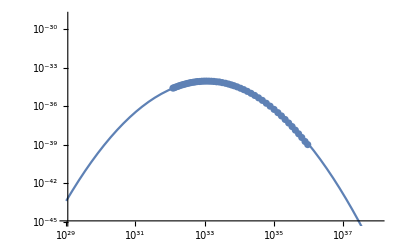

```mathematica
Clear[L0,σ];
F[x_]:=  E^(-(Log10[x]-Log10[L0])^2/(2σ^2))   Log10[E]/(σ Sqrt[2 Pi] x);


L0=0.88 10^34; 
σ=0.62;


(*F1=NonlinearModelFit[GLC.DiagonalMatrix[{1,1/Normalization}],{F[x],L0>0,σ>0},{{L0,0.83 10^33},{σ,0.62}},x,Tolerance->10^(-12)];
F1["ParameterTable"]*)

Show[ListLogLogPlot[GLC.DiagonalMatrix[{1,1/Normalization}],PlotRange->{{10^29,10^38},{10^-45,10^-29}} ],
LogLogPlot[F[x],{x,10^29,10^38}]
]
```

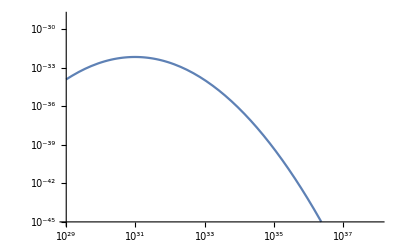

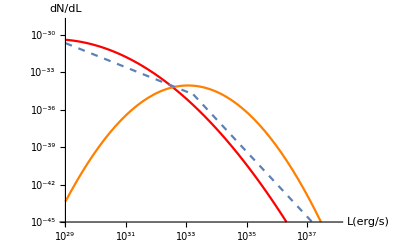

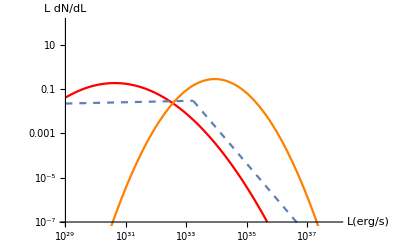

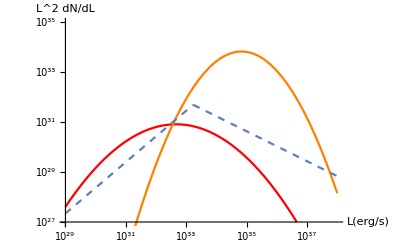

```mathematica
(*AIC, GLC, DISK all together*)
Clear[AIC,GLC,DISK];
AIC[x_]:=  E^(-(Log10[x]-Log10[L0])^2/(2σ^2))   Log10[E]/(σ Sqrt[2 Pi] x);
L0=4.3 10^30;  
σ=0.94;

GLC[x_]:=  E^(-(Log10[x]-Log10[L0G])^2/(2σG^2))   Log10[E]/(σG Sqrt[2 Pi] x);
L0G=0.88 10^34; 
σG=0.62;

DISK[L_]:=((1-n1)(1-n2)/(Lb (n1-n2))) Piecewise[{{(L/Lb)^-n1,L<Lb},{(L/Lb)^-n2,L>Lb}}];
n1=SetPrecision[0.97,20];
n2=SetPrecision[2.60,20];
Lb=SetPrecision[1.7 10^33,20];

GCE[x_]:=  E^(-(Log10[x]-Log10[L0E])^2/(2σE^2))   Log10[E]/(σE Sqrt[2 Pi] x);
L0E=1.3 10^32;
σE=0.7;

LogLogPlot[GCE[x],{x,10^29,10^38},PlotRange->{{10^29,10^38},{10^-45,10^-29}}]

Show[LogLogPlot[AIC[x],{x,10^29,10^38},PlotRange->{{10^29,10^38},{10^-45,10^-29}},AxesLabel->{"L(erg/s)","dN/dL"},PlotStyle->Red,PlotLegends->Placed[{"AIC"},{Right,Top}]],
LogLogPlot[GLC[x],{x,10^29,10^38},PlotRange->{{10^29,10^38},{10^-45,10^-29}},AxesLabel->{{"L(erg/s)"},{"dN/dL"}},PlotStyle->Orange,PlotLegends->Placed[{"GLC"},{Right,Top}]],
LogLogPlot[DISK[x],{x,10^29,10^38},PlotRange->{{10^29,10^38},{10^-45,10^-29}},AxesLabel->{{"L(erg/s)"},{"dN/dL"}},PlotStyle->Dashed,PlotLegends->Placed[{"DISK"},{Right,Top}]]
]
Show[LogLogPlot[x AIC[x],{x,10^29,10^38},PlotRange->{{10^29,10^38},{10^-7,10^2}},AxesLabel->{"L(erg/s)","L dN/dL"},PlotStyle->Red,PlotLegends->Placed[{"AIC"},{Right,Top}] ],
LogLogPlot[x GLC[x],{x,10^29,10^38},PlotStyle->Orange,PlotLegends->Placed[{"GLC"},{Right,Top}]],
LogLogPlot[x DISK[x],{x,10^29,10^38},PlotStyle->Dashed,PlotLegends->Placed[{"DISK"},{Right,Top}] ]     ]

Show[LogLogPlot[x^2 AIC[x],{x,10^29,10^38},PlotRange->{{10^29,10^38},{10^27,10^35}},AxesLabel->{"L(erg/s)","L^2 dN/dL"},PlotStyle->Red,PlotLegends->Placed[{"AIC"},{Right,Top}]],
LogLogPlot[x^2 GLC[x],{x,10^29,10^38},PlotStyle->Orange,PlotLegends->Placed[{"GLC"},{Right,Top}]],
LogLogPlot[x^2 DISK[x],{x,10^29,10^38},PlotStyle->Dashed,PlotLegends->Placed[{"DISK"},{Right,Top}]]]
```

```mathematica
(*FIND NGCE [COMPLETE MODEL]*)
(*DISK has different limits of integration 1e30 and 1e37*)
Clear[kpc,cm,R0,rc,ρ,rLat,FGCE,NGCE,A,Nr,Normalization,sol,Func];
FGCE=1.8 10^-9;
R0=8.5 kpc; (*If we assume all MSPs are in the galactic center*)
rc=20 kpc;
kpc=3.086 10^21 cm;
cm=1;
ρ[r_]:=(r/rc)^(-2γ)  (1+r/rc)^(-6+2 γ);
γ=1.2;
rLat[s_,b_,l_]:=Sqrt[R0^2+s^2-2 R0 s Cos[b] Cos[l]];
Lmin=10^30;
Lmax=10^37;
wp=50;
Normalization=NIntegrate[DISK[L],{L,Lmin,Lmax},WorkingPrecision->wp,PrecisionGoal->10,MinRecursion->9];
Func[L_]:=DISK[L]/Normalization;
L0=4.3 10^32;
Lth=10^34;

(*,Method->"GlobalAdaptive",MinRecursion->6; Method->"Trapezoidal"*)
sol=NSolve[A NIntegrate[x Func[x] ,{x,Lmin,Lmax},MinRecursion->9,WorkingPrecision->wp,PrecisionGoal->10]  NIntegrate[ ρ[rLat[s,b,l]] Cos[b] UnitStep[Abs[b]-2 Degree],{s,0,Infinity},{b,-20 Degree,20 Degree},{l,0,20 Degree},Method->"GlobalAdaptive"]/(4 Pi)-FGCE==0,A]  
NGCE= NIntegrate[s^2 ρ[rLat[s,b,l]] Cos[b] UnitStep[Abs[b]-2 Degree],{s,0,Infinity},{b,-20 Degree,20 Degree},{l,0,20 Degree}] A/.sol
(*Nr=NIntegrate[Func[x]  s^2 ρ[rLat[s,b,l]] Sin[b],{x,4 Pi s^2 Fth,Lmax}, {s,0,Infinity},{b,2 Degree,20 Degree},{l,-20  Degree,20 Degree},Method->"GlobalAdaptive",MinRecursion->8] A/.sol*)


Clear[NGCE];
sol=NSolve[NGCE NIntegrate[x Func[x],{x,Lmin,Lmax},MinRecursion->9,WorkingPrecision->wp,AccuracyGoal->Infinity,PrecisionGoal->30]== FGCE/(1.11 10^-46),NGCE]
Nr=NGCE NIntegrate[Func[x],{x,Lth,Lmax},MinRecursion->9,WorkingPrecision->wp,AccuracyGoal->Infinity,PrecisionGoal->30] /.sol
Rr=NGCE NIntegrate[x Func[x],{x,Lth,Lmax},MinRecursion->9,WorkingPrecision->wp,AccuracyGoal->Infinity,PrecisionGoal->30]/(FGCE/(1.11 10^-46)) /.sol
```

NIntegrate::precw: The precision of the argument function (1.73222663298448368×10^-35 (Piecewise[{{(1.71212494073889547×10^32)/L^0.96999999999999997335, L<1.6999999999999999651×10^33}, {(2.5070742458710073×10^86)/L^2.6000000000000000888, L>1.6999999999999999651×10^33}, {0, True}}])) is less than WorkingPrecision (50.).

NIntegrate::precw: The precision of the argument function (8.06699285770772842×10^-35 x (Piecewise[{{(1.71212494073889547×10^32)/x^0.96999999999999997335, x<1.6999999999999999651×10^33}, {(2.5070742458710073×10^86)/x^2.6000000000000000888, x>1.6999999999999999651×10^33}, {0, True}}])) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{A→6.13356×10^-65}}

{26577.6}

NIntegrate::precw: The precision of the argument function (8.06699285770772842×10^-35 x (Piecewise[{{(1.71212494073889547×10^32)/x^0.96999999999999997335, x<1.6999999999999999651×10^33}, {(2.5070742458710073×10^86)/x^2.6000000000000000888, x>1.6999999999999999651×10^33}, {0, True}}])) is less than WorkingPrecision (50.).

{{NGCE→26468.}}

NIntegrate::precw: The precision of the argument function (8.06699285770772842×10^-35 (Piecewise[{{(1.71212494073889547×10^32)/x^0.96999999999999997335, x<1.6999999999999999651×10^33}, {(2.5070742458710073×10^86)/x^2.6000000000000000888, x>1.6999999999999999651×10^33}, {0, True}}])) is less than WorkingPrecision (50.).

{133.19}

NIntegrate::precw: The precision of the argument function (8.06699285770772842×10^-35 x (Piecewise[{{(1.71212494073889547×10^32)/x^0.96999999999999997335, x<1.6999999999999999651×10^33}, {(2.5070742458710073×10^86)/x^2.6000000000000000888, x>1.6999999999999999651×10^33}, {0, True}}])) is less than WorkingPrecision (50.).

{0.216697}

```mathematica
(*Let's see most effective NIntegrate method for the flux:*)
NIntegrate[Func[x],{x,Lth,Lmax},Method->"GlobalAdaptive",MinRecursion->8,WorkingPrecision->10]
NIntegrate[Func[x],{x,Lth,Lmax},Method->"Trapezoidal",WorkingPrecision->10]

NIntegrate[x Func[x],{x,Lth,Lmax},Method->"GlobalAdaptive",MinRecursion->8,WorkingPrecision->20]
NIntegrate[x Func[x],{x,Lth,Lmax},Method->"Trapezoidal",WorkingPrecision->20]
```

0.005032131739

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in x in the region {{1.×10^34,1.×10^37}}. NIntegrate obtained 0.005134282063 and 0.0002899383947 for the integral and error estimates.

0.005134282063

NIntegrate::precw: The precision of the argument function (8.06699×10^-35 x (Piecewise[{{(1.71212×10^32)/x^0.97, x<1.7×10^33}, {(2.50707×10^86)/x^2.6, x>1.7×10^33}, {0, True}}])) is less than WorkingPrecision (20.).

1.3206548816890346321×10^32

NIntegrate::precw: The precision of the argument function (8.06699×10^-35 x (Piecewise[{{(1.71212×10^32)/x^0.97, x<1.7×10^33}, {(2.50707×10^86)/x^2.6, x>1.7×10^33}, {0, True}}])) is less than WorkingPrecision (20.).

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in x in the region {{1.×10^34,1.×10^37}}. NIntegrate obtained 1.3269821238743741498×10^32 and 1.8377073733019429246×10^30 for the integral and error estimates.

1.3269821238743741498×10^32

```mathematica
(*Mathematica Analytical Integration*)
Clear[Func1,Func2];
Lmax=10^37;
Lmin=10^30;
Func1[x_]=Integrate[DISK[x],x,PrincipalValue->True]
Func2[x_]=Integrate[x DISK[x],x,PrincipalValue->True]
```

Piecewise[{{0.098859614044829852 x^(3/100), x≤1.7×10^33}, {0.999999999999999-(2.7142629872295304×10^51)/x^(8/5), True}}]

Piecewise[{{0.0028794062343154326 x^(103/100), x≤1.7×10^33}, {1.3203883495145689×10^32-(7.2380346326120811×10^51)/x^(3/5), True}}]

```mathematica
(*DISK*)
Clear[Func1,Func2,sol];
Func1[x_]=Piecewise[{{0.09885961404482985227507907688753985924`17.622165863203378 x^(3/100), x≤1.699999999999999965123967908315136`17.622165863203378*^33}, {0.99999999999999899730512831691373411953`17.622165863203378-(2.71426298722953040738275006125549`17.622165863203378*^51)/x^(8/5), x>1.699999999999999965123967908315136`20.*^33}}];
Func2[x_]=Piecewise[{{0.00287940623431543259053628379284096677`17.622165863203378 x^(103/100), x≤1.699999999999999965123967908315136`17.622165863203378*^33}, {1.32038834951456891187703489240799`17.622165863203374*^32-(7.23803463261208108635400016334794`17.622165863203378*^51)/x^(3/5), x>1.699999999999999965123967908315136`20.*^33}}];
sol=Solve[NGCE( Func2[Lmax]-Func2[Lmin])/( Func1[Lmax]-Func1[Lmin])-FGCE/(1.11 10^-46)==0,NGCE]
NGCE ( Func1[Lmax]-Func1[Lth]) /( Func1[Lmax]-Func1[Lmin])/.sol
```

{{NGCE→26468.}}

{133.19}

```mathematica
(*AIC*)
Clear[Func1,Func2,sol];
Func1[x_]=0.5 Erf[1.530483121504238 (-15.056525930076441+0.2134582356401244 Log[x])];
Func2[x_]=2.237281100841295*^31 Erf[1.530483121504238 (-1.-0.2134582356401244 (70.53616781252089-1. Log[x]))];
sol=Solve[NGCE( Func2[Lmax]-Func2[Lmin])/( Func1[Lmax]-Func1[Lmin])-FGCE/(1.11 10^-46)==0,NGCE]
NGCE ( Func1[Lmax]-Func1[Lth]) /( Func1[Lmax]-Func1[Lmin])/.sol
```

{{NGCE→362409.}}

```mathematica
(*GLC*)
Clear[Func1,Func2,sol];
Func1[x_]:=1/2 Erf[(-Log[L0G]+Log[x])/(√2 σG Log[10])];
Func2[x_]:=(∫ⅇ^(-(-Log[L0G]/Log[10]+Log[x]/Log[10])^2/(2 σG^2))ⅆx)/(√(2 π) σG Log[10]);
L0G=0.88 10^34;
σG=0.62;
sol=Solve[NGCE( Func2[Lmax]-Func2[Lmin])/( Func1[Lmax]-Func1[Lmin])-FGCE/(1.11 10^-46)==0,NGCE]
NGCE ( Func1[Lmax]-Func1[Lth]) /( Func1[Lmax]-Func1[Lmin])/.sol
```

Integrate::ilim: Invalid integration variable or limit(s) in ∞.

Integrate::ilim: Invalid integration variable or limit(s) in 0.

{{NGCE→(1.62162×10^37)/(-0.279449 ∫0ⅆ0+0.279449 ∫0ⅆ∞)}}

{(7.52959×10^36)/(-0.279449 ∫0ⅆ0+0.279449 ∫0ⅆ∞)}

```mathematica
(*Integration By Hand*)
Func1[L_]=(1-n1)(1-n2)/(n1-n2)  Piecewise[{{(L/Lb)^(1-n1) /(1-n1),L<Lb},{(L/Lb)^(1-n2)   /(1-n2)    - (n2-n1)/((1-n1)(1-n2)),L>Lb}}];
Func2[L_]=Lb (1-n1)(1-n2)/(n1-n2) Piecewise[{{(L/Lb)^(2-n1) /(2-n1),L<Lb},{(L/Lb)^(2-n2) /(2-n2)  - (n2-n1)/((2-n1)(2-n2)),L>Lb}}];
(FGCE/(1.11 10^-46))( Func1[Lmax]-Func1[Lmin])  /( Func2[Lmax]-Func2[Lmin])
```

26468.

```mathematica
(1-n1)(1-n2)/((n1-n2)  (1 -n1)  Lb^(1-n1))
Lb (1-n1)(1-n2)/((n1-n2)(2-n1) Lb^(2-n1))
(1-n1)(1-n2)/((n1-n2)  (1 -n2)  Lb^(1-n2))
Lb (1-n1)(1-n2)/((n1-n2)(2-n2) Lb^(2-n2))
```

0.098859614044829764

0.0028794062343154325

-2.7142629872295303×10^51

-7.23803463261208×10^51

```mathematica
Func1[Lb-1]-Func1[Lb+1]
```

0

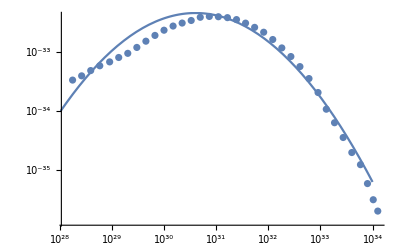

```mathematica
(*IS AIC'S FIT WRONG?*)
Clear[Normalization,AICdata,F,L0,σ];
AICdata={{1.7285085280389353*10^+28,869.7046048151052},{2.5806441939227017*10^+28,1024.8505419673434},{3.8528733573462544*10^+28,1257.4169924823589},{5.752297485529787*10^+28,1513.970583574805},{8.906791157635177*10^+28,1760.2034223491164},{1.3297741095620279*10^+29,2087.082245899236},{1.985338098946716*10^+29,2450.8067088690677},{2.9640879144710884*10^+29,3080.674863508161},{4.4253506087324096*10^+29,3924.876636837752},{6.606999716370757*10^+29,4907.106445743503},{9.864177804575578*10^+29,6004.482736013333},{1.4727108814487576*10^+30,7056.603207827392},{2.198741125014538*10^+30,7922.248011531727},{3.2826962818896025*10^+30,8751.634282040091},{4.9010293920165664*10^+30,9913.73847928088},{7.317182900509915*10^+30,10229.912558898191},{1.0924473476272137*10^+31,10120.389990152678},{1.6310118573837566*10^+31,9772.474832711287},{2.4350827384993167*10^+31,9063.205943387655},{3.635551707667452*10^+31,7900.958231249162},{5.427838656221264*10^+31,6704.879857875086},{8.103703329493255*10^+31,5553.72306702503},{1.2098739813713993*10^+32,4186.721280259344},{1.8063285281829925*10^+32,3023.188222257162},{2.696828596999169*10^+32,2165.460764467862},{4.0263353914409504*10^+32,1465.8631165961833},{6.011274391857447*10^+32,922.7466387318188},{8.974766456618738*10^+32,537.2546040961398},{1.2919819082910342*10^+33,281.39099857955637},{1.8599004881294657*10^+33,166.65158194127613},{2.7266829868599834*10^+33,94.02291156300974},{3.9974182265574376*10^+33,52.53524293885767},{5.860363142697146*10^+33,32.82660440901352},{7.987719636671863*10^+33,15.778147804340168},{1.0308277619948601*10^+34,8.438342849037621},{1.2595470881575635*10^+34,5.4357988562230535}};
Normalization=NIntegrate[Interpolation[AICdata][x],{x,1.8 10^28,1.2 10^34},Method->"GlobalAdaptive",MinRecursion->5];
F[x_]:=  E^(-(Log10[x]-Log10[L0])^2/(2σ^2))   Log10[E]/(σ Sqrt[2 Pi] x);
L0=4.3 10^32;  (*THERE WAS A MISTAKE HERE*)
σ=0.94;
Show[ListLogLogPlot[AICdata.DiagonalMatrix[{1,1/Normalization}]],
LogLogPlot[F[x],{x,10^28,10^34}]]
```